```mathematica
Clear[phystest];
Clear[zero];
Clear[Σ];
Clear[Subscript[a, 1]];
Clear[Subscript[a, 2]];
Clear[Subscript[a, 3]];
Clear[SuperPlus[Subscript[e, 12]]];
Clear[SuperMinus[Subscript[e, 12]]];
Clear[SuperPlus[Subscript[e, 23]]];
Clear[SuperMinus[Subscript[e, 23]]];
Clear[SuperPlus[Subscript[e, 13]]];
Clear[SuperMinus[Subscript[e, 13]]];
Clear[b1];
Clear[b2];
Clear[b3];
Clear[c1];
Clear[c2];
Clear[c3];
Clear[V1];
Clear[V2];
Clear[V3];
```

Clear::ssym: a_1 is not a symbol or a string.

Clear::ssym: a_2 is not a symbol or a string.

Clear::ssym: a_3 is not a symbol or a string.

Clear::ssym: (e_12)^+ is not a symbol or a string.

Clear::ssym: (e_12)^- is not a symbol or a string.

Clear::ssym: (e_23)^+ is not a symbol or a string.

Clear::ssym: (e_23)^- is not a symbol or a string.

Clear::ssym: (e_13)^+ is not a symbol or a string.

Clear::ssym: (e_13)^- is not a symbol or a string.

```mathematica
c1=Table[RandomReal[{1,10}],{i,10^4}];
c2=Table[RandomReal[{1,10}],{i,10^4}];
c3=Table[RandomReal[{1,10}],{i,10^4}];
(*The range of values for C seems to scale the bipartiton graphs at the end*)
```

```mathematica
a1=Table[c1[[i]]-1,{i,1,Length[c1]}];
a2=Table[c2[[i]]-1,{i,1,Length[c2]}];
a3=Table[c3[[i]]-1,{i,1,Length[c3]}];

(*these values a1,a2,a3 are all greater than 0*)

c1[[1]]
a1[[1]]
```

9.14983

8.14983

```mathematica
a1;
```

```mathematica
a2;
```

```mathematica
a3;
```

```mathematica
b1={};
b2={};
b3={};
```

```mathematica
Do[If[Abs[a1[[i]]-a2[[i]]]<a3[[i]]<a1[[i]]+a2[[i]]&&Abs[a1[[i]]-a3[[i]]]<a2[[i]]<a1[[i]]+a3[[i]]
&&Abs[a2[[i]]-a3[[i]]]<a1[[i]]<a2[[i]]+a3[[i]]
,Print[{i ,a1[[i]],a2[[i]],a3[[i]]}],Print["NO"]]
,{i,1,Length[a1]}];

(*Only currently evaluating the first inequality, need to refine the values of aj[[i]] more to include the second 2 inequalities also.*)
```

```mathematica
Do[If[Abs[a1[[i]]-a2[[i]]]<a3[[i]]<a1[[i]]+a2[[i]]&&Abs[a1[[i]]-a3[[i]]]<a2[[i]]<a1[[i]]+a3[[i]]
&&Abs[a2[[i]]-a3[[i]]]<a1[[i]]<a2[[i]]+a3[[i]]
,AppendTo[b1,a1[[i]]]&&AppendTo[b2,a2[[i]]]&&AppendTo[b3,a3[[i]]];]
,{i,1,Length[a1]}];
```

```mathematica
b1
```

```mathematica
b2;
```

```mathematica
b3;
```

```mathematica
Subscript[a, 1]=Table[b1[[i]]+1,{i,1,Length[b1]}];
Subscript[a, 2]=Table[b2[[i]]+1,{i,1,Length[b2]}];
Subscript[a, 3]=Table[b3[[i]]+1,{i,1,Length[b3]}];
```

```mathematica
Subscript[a, 1];
```

```mathematica
SuperPlus[Subscript[e, 12]]=Table[
(√(((Subscript[a, 1][[i]]-Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]-1)^2)((Subscript[a, 1][[i]]-Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]+1)^2))+√(((Subscript[a, 1][[i]]+Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]-1)^2)((Subscript[a, 1][[i]]+Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]+1)^2)))/(4 √(Subscript[a, 1][[i]]Subscript[a, 2][[i]])),{i,1,Length[Subscript[a, 1]]}]//FullSimplify;
SuperMinus[Subscript[e, 12]]=Table[
(√(((Subscript[a, 1][[i]]-Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]-1)^2)((Subscript[a, 1][[i]]-Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]+1)^2))-√(((Subscript[a, 1][[i]]+Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]-1)^2)((Subscript[a, 1][[i]]+Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]+1)^2)))/(4 √(Subscript[a, 1][[i]]Subscript[a, 2][[i]])),{i,1,Length[Subscript[a, 1]]}]//FullSimplify;
SuperPlus[Subscript[e, 23]]=Table[
(√(((Subscript[a, 2][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]-1)^2)((Subscript[a, 2][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]+1)^2))+√(((Subscript[a, 2][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]-1)^2)((Subscript[a, 2][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]+1)^2)))/(4 √(Subscript[a, 2][[i]]Subscript[a, 3][[i]])),{i,1,Length[Subscript[a, 1]]}]//FullSimplify;
SuperMinus[Subscript[e, 23]]=Table[
(√(((Subscript[a, 2][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]-1)^2)((Subscript[a, 2][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]+1)^2))-√(((Subscript[a, 2][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]-1)^2)((Subscript[a, 2][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]+1)^2)))/(4 √(Subscript[a, 2][[i]]Subscript[a, 3][[i]])),{i,1,Length[Subscript[a, 1]]}]//FullSimplify;
SuperPlus[Subscript[e, 13]]=Table[
(√(((Subscript[a, 1][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]-1)^2)((Subscript[a, 1][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]+1)^2))+√(((Subscript[a, 1][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]-1)^2)((Subscript[a, 1][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]+1)^2)))/(4 √(Subscript[a, 1][[i]]Subscript[a, 3][[i]])),{i,1,Length[Subscript[a, 1]]}]//FullSimplify;
SuperMinus[Subscript[e, 13]]=Table[
(√(((Subscript[a, 1][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]-1)^2)((Subscript[a, 1][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]+1)^2))-√(((Subscript[a, 1][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]-1)^2)((Subscript[a, 1][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]+1)^2)))/(4 √(Subscript[a, 1][[i]]Subscript[a, 3][[i]])),{i,1,Length[Subscript[a, 1]]}]//FullSimplify;
```

```mathematica
Subscript[σ, SF]=Table[{{Subscript[a, 1][[i]],0,SuperPlus[Subscript[e, 12]][[i]],0, SuperPlus[Subscript[e, 13]][[i]],0},{0,Subscript[a, 1][[i]],0,SuperMinus[Subscript[e, 12]][[i]],0,SuperMinus[Subscript[e, 13]][[i]]},{SuperPlus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0, SuperPlus[Subscript[e, 23]][[i]],0},{0,SuperMinus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0,SuperMinus[Subscript[e, 23]][[i]]},{SuperPlus[Subscript[e, 13]][[i]],0,SuperPlus[Subscript[e, 23]][[i]],0, Subscript[a, 3][[i]],0},{0,SuperMinus[Subscript[e, 13]][[i]],0,SuperMinus[Subscript[e, 23]][[i]],0,Subscript[a, 3][[i]]}},{i,1,Length[Subscript[a, 1]]}];
```

```mathematica
Subscript[σ, SF][[1]]
```

{{3.27908,0,5.02462,0,4.48209,0},{0,3.27908,0,-3.16657,0,1.37401},{5.02462,0,8.5656,0,7.74919,0},{0,-3.16657,0,8.5656,0,-7.28576},{4.48209,0,7.74919,0,7.16242,0},{0,1.37401,0,-7.28576,0,7.16242}}

```mathematica
Eigenvalues[Subscript[σ, SF][[1]]]
```

{22.6036,15.9576,6.81115,0.146818,0.0626659,0.0442408}

```mathematica
(*All eigenvalues now real and positive therefore we have physical states*)
```

```mathematica
Subscript[σ, PT1]=Table[{{Subscript[a, 1][[i]],0,SuperPlus[Subscript[e, 12]][[i]],0, SuperPlus[Subscript[e, 13]][[i]],0},{0,Subscript[a, 1][[i]],0,-SuperMinus[Subscript[e, 12]][[i]],0,-SuperMinus[Subscript[e, 13]][[i]]},{SuperPlus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0, SuperPlus[Subscript[e, 23]][[i]],0},{0,-SuperMinus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0,SuperMinus[Subscript[e, 23]][[i]]},{SuperPlus[Subscript[e, 13]][[i]],0,SuperPlus[Subscript[e, 23]][[i]],0, Subscript[a, 3][[i]],0},{0,-SuperMinus[Subscript[e, 13]][[i]],0,SuperMinus[Subscript[e, 23]][[i]],0,Subscript[a, 3][[i]]}},{i,1,Length[Subscript[a, 1]]}];
(*Subscript[σ, PT1]=Subscript[P1σ, SF] P1 calculated by hand*)
```

```mathematica
Subscript[σ, PT1][[1]]
```

{{3.27908,0,5.02462,0,4.48209,0},{0,3.27908,0,3.16657,0,-1.37401},{5.02462,0,8.5656,0,7.74919,0},{0,3.16657,0,8.5656,0,-7.28576},{4.48209,0,7.74919,0,7.16242,0},{0,-1.37401,0,-7.28576,0,7.16242}}

```mathematica
Length[Subscript[σ, PT1]]
```

5044

```mathematica
Subscript[σ, PT2]=Table[{{Subscript[a, 1][[i]],0,SuperPlus[Subscript[e, 12]][[i]],0, SuperPlus[Subscript[e, 13]][[i]],0},{0,Subscript[a, 1][[i]],0,-SuperMinus[Subscript[e, 12]][[i]],0,SuperMinus[Subscript[e, 13]][[i]]},{SuperPlus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0, SuperPlus[Subscript[e, 23]][[i]],0},{0,-SuperMinus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0,-SuperMinus[Subscript[e, 23]][[i]]},{SuperPlus[Subscript[e, 13]][[i]],0,SuperPlus[Subscript[e, 23]][[i]],0, Subscript[a, 3][[i]],0},{0,SuperMinus[Subscript[e, 13]][[i]],0,-SuperMinus[Subscript[e, 23]][[i]],0,Subscript[a, 3][[i]]}},{i,1,Length[Subscript[a, 1]]}];
```

```mathematica
(*Subscript[σ, PT2]=Subscript[P2σ, SF] P2 calculated by hand*)
```

```mathematica
Subscript[σ, PT3]=Table[{{Subscript[a, 1][[i]],0,SuperPlus[Subscript[e, 12]][[i]],0, SuperPlus[Subscript[e, 13]][[i]],0},{0,Subscript[a, 1][[i]],0,SuperMinus[Subscript[e, 12]][[i]],0,-SuperMinus[Subscript[e, 13]][[i]]},{SuperPlus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0, SuperPlus[Subscript[e, 23]][[i]],0},{0,SuperMinus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0,-SuperMinus[Subscript[e, 23]][[i]]},{SuperPlus[Subscript[e, 13]][[i]],0,SuperPlus[Subscript[e, 23]][[i]],0, Subscript[a, 3][[i]],0},{0,-SuperMinus[Subscript[e, 13]][[i]],0,-SuperMinus[Subscript[e, 23]][[i]],0,Subscript[a, 3][[i]]}},{i,1,Length[Subscript[a, 1]]}];
```

```mathematica
(*Subscript[σ, PT2]=Subscript[P2σ, SF] P2 calculated by hand*)
```

```mathematica
zero={{0,0},{0,0}};
Σ=ArrayFlatten[{{ⅈ PauliMatrix[2],zero,zero},{zero,ⅈ PauliMatrix[2],zero},{zero,zero,ⅈ PauliMatrix[2]}}]
```

{{0,1,0,0,0,0},{-1,0,0,0,0,0},{0,0,0,1,0,0},{0,0,-1,0,0,0},{0,0,0,0,0,1},{0,0,0,0,-1,0}}

```mathematica
V1={};
Do[AppendTo[V1,Min[Abs[Eigenvalues[ⅈ Σ . Subscript[σ, PT1][[i]]//Chop]]]];,{i,1,Length[Subscript[σ, PT1]]}]
```

```mathematica
V1[[1]]
```

0.0626085

```mathematica
V2={};
Do[AppendTo[V2,Min[Abs[Eigenvalues[ⅈ Σ . Subscript[σ, PT2][[i]]//Chop]]]];,{i,1,Length[Subscript[σ, PT2]]}]
```

```mathematica
V3={};
Do[AppendTo[V3,Min[Abs[Eigenvalues[ⅈ Σ . Subscript[σ, PT3][[i]]//Chop]]]];,{i,1,Length[Subscript[σ, PT3]]}]
```

```mathematica
Table[{i,V1[[i]]},{i,1,Length[V1]}];
Table[{i,V2[[i]]},{i,1,Length[V2]}];
Table[{i,V3[[i]]},{i,1,Length[V3]}];
```

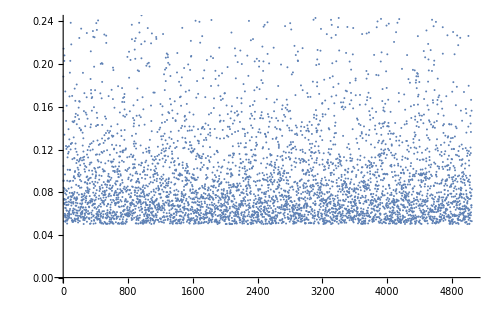

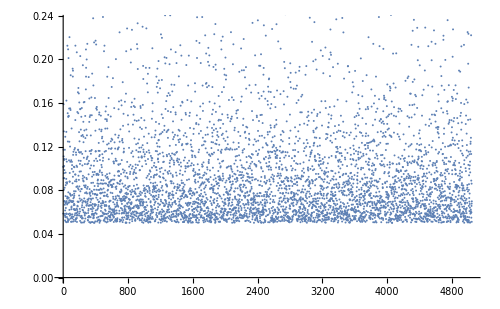

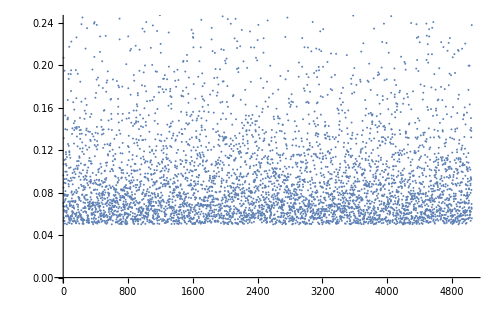

```mathematica
ListPlot[Table[{i,V1[[i]]},{i,1,Length[V1]}]]
ListPlot[Table[{i,V2[[i]]},{i,1,Length[V2]}]]
ListPlot[Table[{i,V3[[i]]},{i,1,Length[V3]}]]
```

```mathematica
(*The values on the Y-axis scale along with the range of values at the very start initially chosen for c
i.e. if I chose values between 1 and 10 then the points converge to 1/(2(upper limit)) i.e.*)
```

```mathematica
covmpt=Table[{{a[[i]],0,cp[[i]],0},{0,a[[i]],0,-cm[[i]]},{cp[[i]],0,b[[i]],0},{0,-cm[[i]],0,b[[i]]}},{i,10^5}];
```

```mathematica
(*partially transposed cov matrix)
```

```mathematica
phystest2={};
Do[AppendTo[phystest2,{Abs[Eigenvalues[ⅈ Σ . covmpt[[i]]//Chop]]}];,{i,1,Length[covmpt]}]


phystest2[[200]]
```

{{144.562,144.562,0.948294,0.948294}}

```mathematica
Table[{i,{Min[phystest2[[i]]]}},{i,1,Length[cm]}];
Min[phystest2[[1]]]
```

0.258571

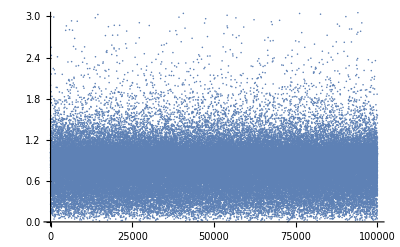

```mathematica
ListPlot[Table[{i,Min[phystest2[[i]]]},{i,10^5}],PlotRange->{0,3}]
(*Points that are less than 1 are entangled and greater than one are seperable*)
```

```mathematica
SympEig={};
Do[AppendTo[SympEig,Min[Abs[Eigenvalues[ⅈ Σ . covmpt[[i]]]]//Chop]];,{i,10^5}];
```

```mathematica
Dynamic[i]
```

```mathematica
SympEig[[1]]
```

0.504792

```mathematica
Table[{i,{SympEig[[i]]}},{i,10^5}];
```

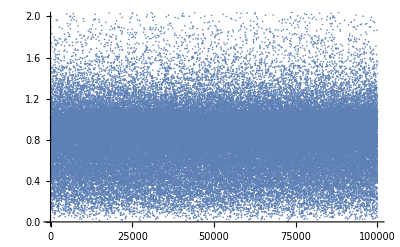

```mathematica
ListPlot[Table[{i,SympEig[[i]]},{i,10^5}],PlotRange->{0,2}]
```

```mathematica
Negativity={};
Do[AppendTo[Negativity,(1-SympEig[[i]])/(2SympEig[[i]])];,{i,10^5}];
Negativity[[1]]
```

1.4337

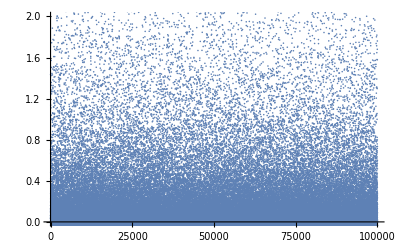

```mathematica
Table[{i,{Negativity[[i]]}},{i,10^5}];
ListPlot[Table[{i,Negativity[[i]]},{i,10^5}],PlotRange->{0,2}]
```

```mathematica
LogNeg={};
Do[AppendTo[LogNeg,-Log[SympEig[[i]]]];,{i,10^5}];
LogNeg[[1]]
```

1.35258

```mathematica
Dynamic[i]
```

```mathematica
Table[{i,{LogNeg[[i]]}},{i,10^5}];
```

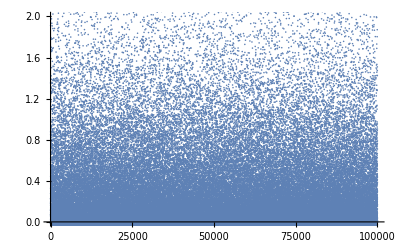

```mathematica
ListPlot[Table[{i,LogNeg[[i]]},{i,10^5}],PlotRange->{0,2}]
```

```mathematica
Subscript[Determinantσ, P.T]={};
```

```mathematica
Do[AppendTo[Subscript[Determinantσ, P.T],(a[[i]]b[[i]]-cp[[i]]^2)(a[[i]]b[[i]]-cm[[i]]^2)];,{i,10^5}];
Subscript[Determinantσ, P.T][[1]]
```

951.141

```mathematica
Table[{i,{Determinantσ[[i]]}},{i,10^5}];
```

```mathematica
Purity={};
```

```mathematica
Do[AppendTo[Purity,1/(√(Subscript[Determinantσ, P.T][[i]]))];,{i,10^5}];
```

```mathematica
Purity[[1]]
```

0.0108912

```mathematica
Table[{i,{Purity[[i]]}},{i,10^5}];
```

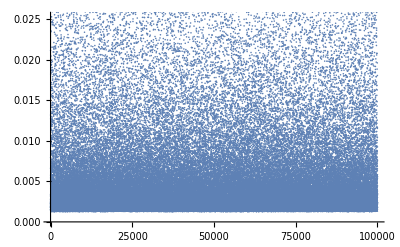

```mathematica
ListPlot[Table[{i,Purity[[i]]},{i,10^5}]]
```

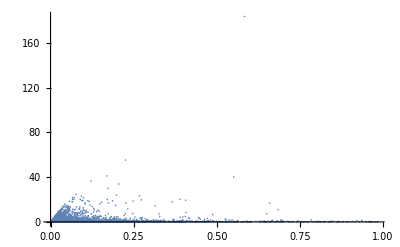

```mathematica
ListPlot[Table[{Purity[[i]],Max[0,Negativity[[i]]]},{i,10^5}],PlotRange->All]
(*Yesterday max value on y axis was about 40, now is nearly 200*)
```

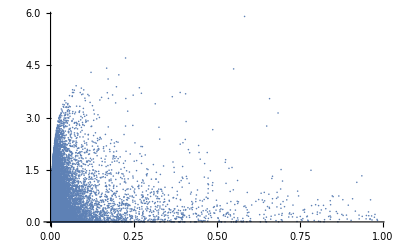

```mathematica
ListPlot[Table[{Purity[[i]],Max[0,LogNeg[[i]]]},{i,10^5}],PlotRange->All]
(*Yesterday max value on y axis was about 4, now is around 6*)
```